```mathematica
SetDirectory[NotebookDirectory[]]
countsRaw=Import["protein_based_rec_scores_counts.tsv"];
Length[countsRaw]
counts=countsRaw;
counts[[All,8;;14]]=ToExpression/@ countsRaw[[All,8;;14]];
talliedCounts=GatherBy[counts,{#[[1]],#[[6]],#[[14]],#[[15]]}&];
```

/Users/hayssam/Documents/ISOP_0.2/tests

1024

Statistics about the data

```mathematica
Grid[Sort[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedCounts]]
```

ar | 186 | LSI | 25%Prot,25%Docs | 30
ar | 186 | LSI+STRING | 25%Prot,25%Docs | 30
ar | 9630 | LSI | 25%Prot,25%Docs | 30
ar | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
egfr | 334 | LSI | 25%Prot,25%Docs | 30
egfr | 334 | LSI+STRING | 25%Prot,25%Docs | 30
egfr | 9630 | LSI | 25%Prot,25%Docs | 30
egfr | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
hsa04010 | 328 | LSI | 25%Prot,25%Docs | 21
hsa04010 | 328 | LSI+STRING | 25%Prot,25%Docs | 21
hsa04010 | 9630 | LSI | 25%Prot,25%Docs | 22
hsa04010 | 9630 | LSI | 25%Prot,KEGG REFS | 18
hsa04010 | 9630 | LSI | TF+MEMB | 1
hsa04010 | 9630 | LSI+STRING | 25%Prot,25%Docs | 22
hsa04010 | 9630 | LSI+STRING | 25%Prot,KEGG REFS | 18
hsa04010 | 9630 | LSI+STRING | TF+MEMB | 1
hsa04012 | 208 | LSI | 25%Prot,25%Docs | 23
hsa04012 | 208 | LSI+STRING | 25%Prot,25%Docs | 23
hsa04012 | 9630 | LSI | 25%Prot,25%Docs | 24
hsa04012 | 9630 | LSI | 25%%Prot,KEGG REFS | 11
hsa04012 | 9630 | LSI | TF+MEMB | 1
hsa04012 | 9630 | LSI+STRING | 25%Prot,25%Docs | 24
hsa04012 | 9630 | LSI+STRING | 25%%Prot,KEGG REFS | 11
hsa04012 | 9630 | LSI+STRING | TF+MEMB | 1
il2 | 43 | LSI | 25%Prot,25%Docs | 31
il2 | 43 | LSI+STRING | 25%Prot,25%Docs | 31
il2 | 157 | LSI | 25%Prot,25%Docs | 30
il2 | 157 | LSI+STRING | 25%Prot,25%Docs | 30
il2 | 9630 | LSI | 25%Prot,25%Docs | 30
il2 | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
tcell | 242 | LSI | 25%Prot,25%Docs | 30
tcell | 242 | LSI+STRING | 25%Prot,25%Docs | 30
tcell | 9630 | LSI | 25%Prot,25%Docs | 30
tcell | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
tgfb | 344 | LSI | 25%Prot,25%Docs | 30
tgfb | 344 | LSI+STRING | 25%Prot,25%Docs | 30
tgfb | 9630 | LSI | 25%Prot,25%Docs | 30
tgfb | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
tnf | 338 | LSI | 25%Prot,25%Docs | 30
tnf | 338 | LSI+STRING | 25%Prot,25%Docs | 30
tnf | 9630 | LSI | 25%Prot,25%Docs | 30
tnf | 9630 | LSI+STRING | 25%Prot,25%Docs | 30

```mathematica
cid=-1;
```

Plot true edges against total edges

```mathematica
xlimE=counts[[cid,5]]*3
xlimProt=counts[[cid,4]]*3
ylimE=counts[[cid,5]]*1.5
ylimProt=counts[[cid,4]]*1.5
```

288

129

144.

64.5

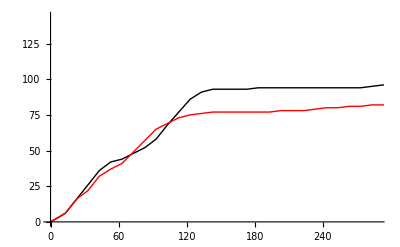

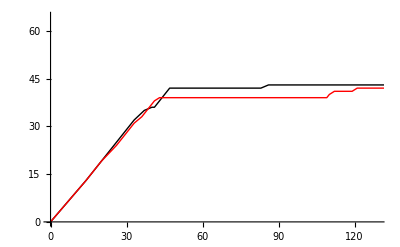

```mathematica
edgesPoints=Partition[Riffle[counts[[cid,11]],counts[[cid,12]]],2];
proteinPoints=Partition[Riffle[counts[[cid,8]],counts[[cid,9]]],2];
edgesPointsString=Partition[Riffle[counts[[cid-1,11]],counts[[cid-1,12]]],2];
proteinPointsString=Partition[Riffle[counts[[cid-1,8]],counts[[cid-1,9]]],2];
ListLinePlot[{edgesPoints,edgesPointsString},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->{Black,Red}]
ListLinePlot[{proteinPoints,proteinPointsString},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->{Black,Red}]
```

ROC curves

```mathematica
cid
```

-1

```mathematica
RocStyle={Black,Red,{Gray,Dashed}};
```

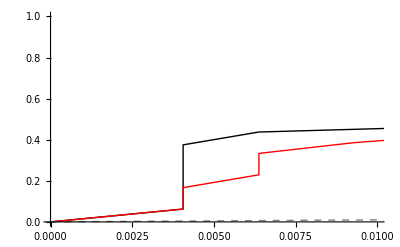

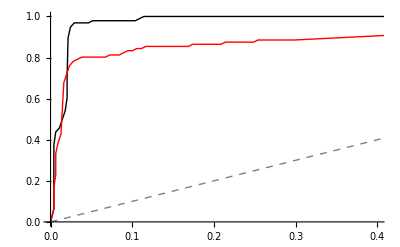

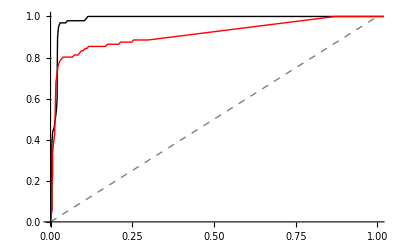

```mathematica
tpr=counts[[cid,12]]/counts[[cid,5]];
fpr=counts[[cid,13]]/counts[[cid,7]];
roc=Partition[Riffle[fpr,tpr],2];
tprString=counts[[cid-1,12]]/counts[[cid-1,5]];
fprString=counts[[cid-1,13]]/counts[[cid-1,7]];
rocString=Partition[Riffle[fprString,tprString],2];

ListLinePlot[{roc,rocString,{{0,0},{1,1}}},PlotRange->{{0,0.01},{0,1}},PlotStyle->RocStyle]
ListLinePlot[{roc,rocString,{{0,0},{1,1}}},PlotRange->{{0,0.4},{0,1}},PlotStyle->RocStyle]
ListLinePlot[{roc,rocString,{{0,0},{1,1}}},PlotRange->{{0,1},{0,1}},PlotStyle->RocStyle]
```

## Function to plot a single result

```mathematica
countStyle={Black,Red,Dashed,Dashed};
```

```mathematica
PlotRowForCid[cid_]:=Module[{label,realPosEdges,realPosProt,possibleProt,possibleEdges,xlimE,xlimProt,ylimE,ylimProt,neighborStr,optimalCurveEdges,optimalCurveProt,chancePickingPositiveEdge,chancePickingPositiveProt,edgesPoints,proteinPoints,edgesPointsString,proteinPointsString,tpr,fpr,roc,tprString,fprString,rocString},
label=counts[[cid,1]];
realPosEdges=counts[[cid,5]];
realPosProt=counts[[cid,4]];
possibleProt=counts[[cid,6]];
possibleEdges=counts[[cid,7]];
xlimE=counts[[cid,5]]*3;
xlimProt=counts[[cid,4]]*3;
ylimE=counts[[cid,5]]*1.5;
ylimProt=counts[[cid,4]]*1.5;
neighborStr=If[possibleProt>9000,"Whole","In neighbor"];
optimalCurveEdges={{0,0},{realPosEdges,realPosEdges},{10000,realPosEdges}};
optimalCurveProt={{0,0},{realPosProt,realPosProt},{10000,realPosProt}};
chancePickingPositiveEdge={{0,0},{xlimE,xlimE*realPosEdges/possibleEdges}};
chancePickingPositiveProt={{0,0},{xlimProt,xlimProt*realPosProt/possibleProt}};
edgesPoints=Partition[Riffle[counts[[cid,11]],counts[[cid,12]]],2];
proteinPoints=Partition[Riffle[counts[[cid,8]],counts[[cid,9]]],2];
edgesPointsString=Partition[Riffle[counts[[cid-1,11]],counts[[cid-1,12]]],2];
proteinPointsString=Partition[Riffle[counts[[cid-1,8]],counts[[cid-1,9]]],2];
tpr=counts[[cid,12]]/realPosEdges;
fpr=counts[[cid,13]]/possibleEdges;
roc=Partition[Riffle[fpr,tpr],2];
tprString=counts[[cid-1,12]]/realPosEdges;
fprString=counts[[cid-1,13]]/possibleEdges;
rocString=Partition[Riffle[fprString,tprString],2];

{label,
neighborStr,
ListLinePlot[{edgesPoints,edgesPointsString,optimalCurveEdges,chancePickingPositiveEdge},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->countStyle],
ListLinePlot[{proteinPoints,proteinPointsString,optimalCurveProt,chancePickingPositiveProt},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->countStyle],
ListLinePlot[{roc,rocString,{{0,0},{1,1}}},PlotRange->{{0,0.1},{0,1}},PlotStyle->RocStyle],ListLinePlot[{roc,rocString,{{0,0},{1,1}}},PlotRange->{{0,1},{0,1}},PlotStyle->RocStyle]
}
]
```

```mathematica
GridHeader={"Pathway","Neighborhood","Edges counts","Prot counts","Edge ROC close","Edge ROC Full"};
```

```mathematica
cidStart=600;
Grid[
Prepend[Table[PlotRowForCid[cid],{cid,cidStart,cidStart+20,2}],GridHeader]
,
Background->{None,{Lighter[Black,.95],{{White}}}},
Dividers->{Black,Black},
Alignment->{{Center,{Center}}},
Frame->Darker[Gray,.6]
]
```

## For the PW in the kegg db

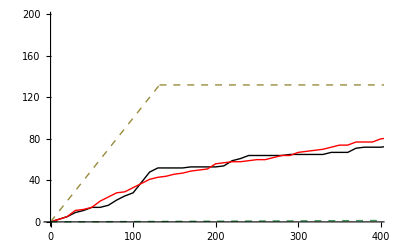
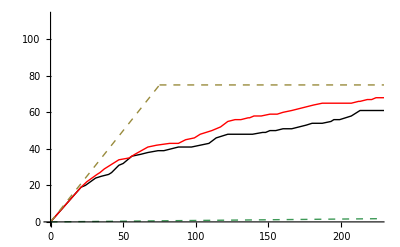
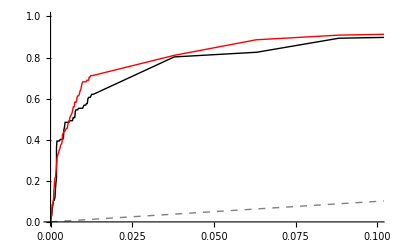
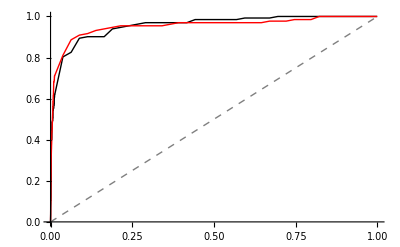
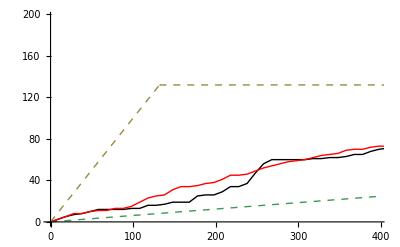
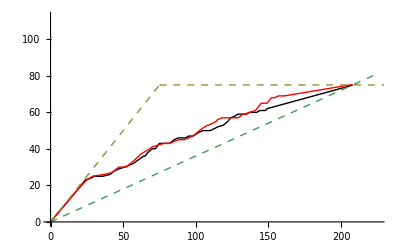
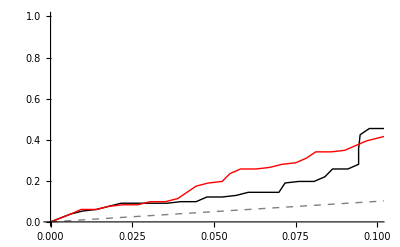
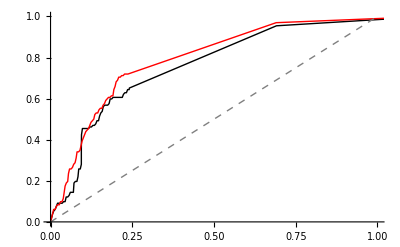
Pathway | Neighborhood | Edges counts | Prot counts | Edge ROC close | Edge ROC Full
hsa04012 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04012 | In neighbor | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | In neighbor | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04012 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04012 | In neighbor | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04012 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04012 | In neighbor | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
keggCID=722;
endCID=Length[countsRaw];
Grid[
Prepend[Table[PlotRowForCid[cid],{cid,keggCID,endCID,2}],GridHeader]
,
Background->{None,{Lighter[Black,.95],{{White}}}},
Dividers->{Black,Black},
Alignment->{{Center,{Center}}},
Frame->Darker[Gray,.6]
]
```

## KEGG pathways with BowTie setup

```mathematica
bowTiekeggCID=740;
```

```mathematica
counts[[bowTiekeggCID]]
```

{hsa04012,{PTK2,CBL,JUN,ELK1,MYC,STAT5A,STAT5B,CDKN1A,CDKN1B,GSK3B,BAD,EIF4EBP1,RPS6KB1,EGFR,ERBB2,ERBB3,ERBB4},{12354693,11877389,16247449,15173068,17426253,10799311,12244301,8247524,11809746,10611223,11173924,11807823,7538656,11278754,17911387,11500516,8087846,12193575,16413544,8798570,16023596,9774445,15784622,11606575,15534001,11500850,12239347,1706616,16767099,16843263},75,132,9630,39500,{0,22,27,32,39,44,49,56,65,71,76,85,91,96,102,110,119,128,136,142,148,155,164,171,177,184,190,195,200,208,216,223,227,237,243,246,253,259,264,271,275,279,286,291,298,303,310,318,322,328,334,341,343,351,357,365,371,377,382,388,1145,1829,2446,2844,3315,3849,4322,4712,5086,5432,5807,6044,6254,6555,6813,7040,7259,7474,7673,7862,8051,8199,8355,8477,8634,8727,8831,8927,9020,9090,9177,9233,9311,9372,9454,9502,9547,9591,9630},{0,20,23,25,29,31,33,35,37,38,39,39,39,40,42,42,42,42,42,43,43,43,44,44,46,46,47,47,47,48,49,49,49,51,51,51,51,51,51,52,52,52,52,52,52,52,52,53,53,54,54,54,54,54,54,56,56,56,56,56,61,66,66,67,67,71,72,72,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75},{0,2,4,7,10,13,16,21,28,33,37,46,52,56,60,68,77,86,94,99,105,112,120,127,131,138,143,148,153,160,167,174,178,186,192,195,202,208,213,219,223,227,234,239,246,251,258,265,269,274,280,287,289,297,303,309,315,321,326,332,1084,1763,2380,2777,3248,3778,4250,4640,5012,5357,5732,5969,6179,6480,6738,6965,7184,7399,7598,7787,7976,8124,8280,8402,8559,8652,8756,8852,8945,9015,9102,9158,9236,9297,9379,9427,9472,9516,9555},{0,21,31,41,51,61,71,81,91,101,111,121,131,141,151,161,171,181,191,201,211,221,231,241,251,261,271,281,291,301,311,321,331,341,351,361,371,381,391,401,411,421,431,441,451,461,471,481,491,501,511,521,531,541,551,561,571,581,591,600,1600,2600,3600,4600,5600,6600,7600,8600,9600,10600,11600,12600,13600,14600,15600,16600,17600,18600,19600,20600,21600,22600,23600,24600,25600,26600,27600,28600,29600,30600,31600,32600,33600,34600,35600,36600,37600,38600,39600},{0,6,9,12,15,20,25,28,30,31,33,33,33,33,34,36,37,37,37,37,37,37,37,37,38,38,38,38,40,40,41,41,41,41,41,41,41,42,43,44,44,44,44,44,44,44,44,44,44,45,45,45,46,46,46,46,46,46,46,46,52,59,59,59,62,74,76,83,110,111,111,111,111,112,113,114,115,115,116,117,119,121,121,122,124,124,125,125,126,127,129,130,130,130,131,131,131,131,132},{0,15,22,29,36,41,46,53,61,70,78,88,98,108,117,125,134,144,154,164,174,184,194,204,213,223,233,243,251,261,270,280,290,300,310,320,330,339,348,357,367,377,387,397,407,417,427,437,447,456,466,476,485,495,505,515,525,535,545,554,1548,2541,3541,4541,5538,6526,7524,8517,9490,10489,11489,12489,13489,14488,15487,16486,17485,18485,19484,20483,21481,22479,23479,24478,25476,26476,27475,28475,29474,30473,31471,32470,33470,34470,35469,36469,37469,38469,39468},LSI,MEMB+TF}

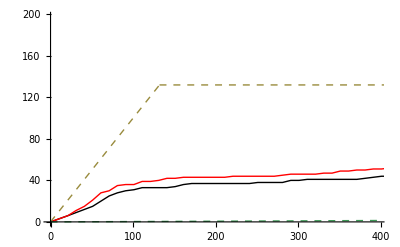
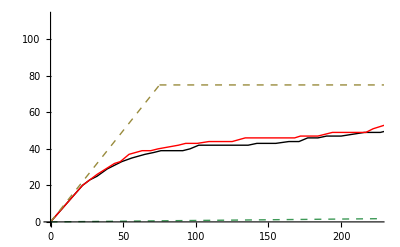
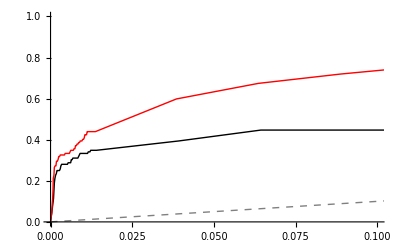
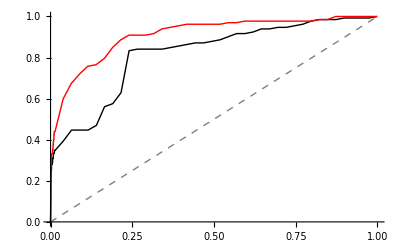
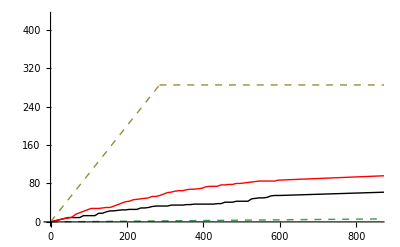
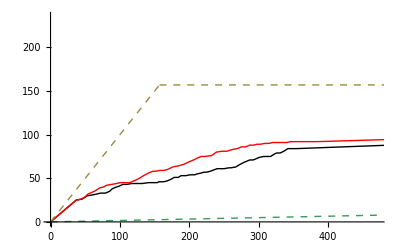
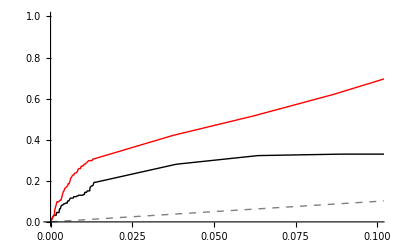
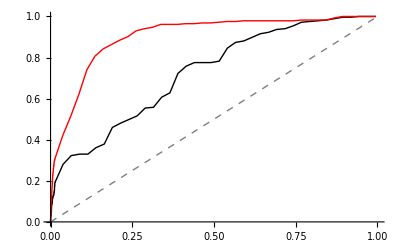
Pathway | Neighborhood | Edges counts | Prot counts | Edge ROC close | Edge ROC Full
hsa04012 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
endCID=Length[countsRaw];
Grid[
Prepend[Table[PlotRowForCid[cid],{cid,bowTiekeggCID,endCID,2}],GridHeader]
,
Background->{None,{Lighter[Black,.95],{{White}}}},
Dividers->{Black,Black},
Alignment->{{Center,{Center}}},
Frame->Darker[Gray,.6]
]
```

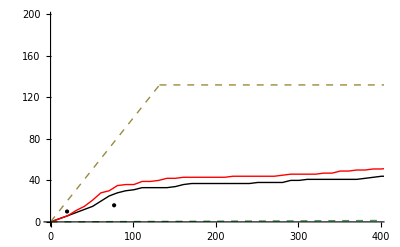

```mathematica
Show[
-Graphics-,Graphics[Point[{{77,16},{20,10}}]]
]
```

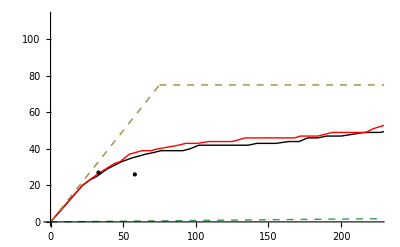

```mathematica
Show[
-Graphics-,Graphics[Point[{{58,26},{33,27}}]]]
```

## Comparing average

We group by PW, possible edges and scoring fun

```mathematica
countStyle={Black,Dashed,Dashed};
RocStyle={Black,Red,{Gray,Dashed}};
```

```mathematica
talliedCounts=GatherBy[counts,{#[[1]],#[[6]],#[[14]],#[[15]]}&];
```

```mathematica
Length[talliedCounts[[1]]]
```

30

```mathematica
Length /@ talliedCounts
```

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,4,4,3,3,1,1,1,1,1,1,1,1}

```mathematica
talliedCounts[[1,All,5]]
```

{87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87}

Plot them all

```mathematica
PlotForRow[row_]:=Module[{label,realPosEdges,realPosProt,possibleProt,possibleEdges,xlimE,xlimProt,ylimE,ylimProt,neighborStr,optimalCurveEdges,optimalCurveProt,chancePickingPositiveEdge,chancePickingPositiveProt,edgesPoints,proteinPoints,edgesPointsString,proteinPointsString,tpr,fpr,roc,tprString,fprString,rocString},
label=row[[1]];
realPosEdges=row[[5]];
realPosProt=row[[4]];
possibleProt=row[[6]];
possibleEdges=row[[7]];
xlimE=row[[5]]*3;
xlimProt=row[[4]]*3;
ylimE=row[[5]]*1.5;
ylimProt=row[[4]]*1.5;
neighborStr=If[possibleProt>9000,"Whole","In neighbor"];
optimalCurveEdges={{0,0},{realPosEdges,realPosEdges},{10000,realPosEdges}};
optimalCurveProt={{0,0},{realPosProt,realPosProt},{10000,realPosProt}};
chancePickingPositiveEdge={{0,0},{xlimE,xlimE*realPosEdges/possibleEdges}};
chancePickingPositiveProt={{0,0},{xlimProt,xlimProt*realPosProt/possibleProt}};
edgesPoints=Partition[Riffle[row[[11]],row[[12]]],2];
proteinPoints=Partition[Riffle[row[[8]],row[[9]]],2];
tpr=row[[12]]/realPosEdges;
fpr=row[[13]]/possibleEdges;
roc=Partition[Riffle[fpr,tpr],2];

{label,
neighborStr,
ListLinePlot[{edgesPoints,optimalCurveEdges,chancePickingPositiveEdge},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->countStyle],
ListLinePlot[{proteinPoints,optimalCurveProt,chancePickingPositiveProt},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->countStyle],
ListLinePlot[{roc,{{0,0},{1,1}}},PlotRange->{{0,0.1},{0,1}},PlotStyle->RocStyle],ListLinePlot[{roc,{{0,0},{1,1}}},PlotRange->{{0,1},{0,1}},PlotStyle->RocStyle]
}
]
```

```mathematica
Grid[
PlotForRow[#]&/@talliedCounts[[1]]
]
```

Plotting them all as a curve?

```mathematica
rows=talliedCounts[[1]];
```

```mathematica
PlotForRows[rows_,style_:{Hue[0.65,0.5,0.8,1],Thick}]:=Module[{label,method,realPosEdges,realPosProt,possibleProt,possibleEdges,nReps,xlimE,optTag,xlimProt,ylimE,ylimProt,neighborStr,optimalCurveProt,chancePickingPositiveEdge,chancePickingPositiveProt,edgesPoints,protsPoints,rocs,optimalCurveEdges},
label=ToUpperCase[rows[[1,1]]];
method=rows[[1,14]];
realPosEdges=rows[[1,5]];
realPosProt=rows[[1,4]];
possibleProt=rows[[1,6]];
possibleEdges=rows[[1,7]];
nReps=Length[rows];
xlimE=rows[[1,5]]*2;
optTag=rows[[1,15]];
xlimProt=rows[[1,4]]*2;
ylimE=rows[[1,5]]*1.25;
ylimProt=rows[[1,4]]*1.25;
neighborStr=If[possibleProt>9000,"HPRD",Grid[{{"Neighborhood"},{StringForm["`` prots",possibleProt]},{StringForm["`` edges",possibleEdges]}}]];optimalCurveEdges={{0,0},{realPosEdges,realPosEdges},{10000,realPosEdges}};
optimalCurveProt={{0,0},{realPosProt,realPosProt},{10000,realPosProt}};
chancePickingPositiveEdge={{0,0},{xlimE,xlimE*realPosEdges/possibleEdges}};
chancePickingPositiveProt={{0,0},{xlimProt,xlimProt*realPosProt/possibleProt}};
edgesPoints=Partition[Riffle[#[[1]],#[[2]]],2]& /@ Transpose[{rows[[All,11,2;;]],rows[[All,12,2;;]]}];
protsPoints=Partition[Riffle[#[[1]],#[[2]]],2]& /@ Transpose[{rows[[All,8,2;;]],rows[[All,9,2;;]]}];
rocs=Partition[Riffle[#[[13,2;;]]/possibleEdges,#[[12,2;;]]/realPosEdges],2]&/@ rows;
{
label,
neighborStr,
method,
optTag,
nReps,
Show[
ListLinePlot[{optimalCurveEdges,chancePickingPositiveEdge},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->{Dashed,Dashed}],
ListLinePlot[edgesPoints,PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->style]
],
Show[
ListLinePlot[{optimalCurveProt,chancePickingPositiveProt},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->{Dashed,Dashed}],
ListLinePlot[protsPoints,PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->style]
],
Show[
ListLinePlot[{{0,0},{1,1}},PlotRange->{{0,0.1},{0,1}},PlotStyle->Dashed],
ListLinePlot[rocs,PlotRange->{{0,0.1},{0,1}},PlotStyle->style]
],
Show[
ListLinePlot[{{0,0},{1,1}},PlotRange->{{0,1},{0,1}},PlotStyle->Dashed],
ListLinePlot[rocs,PlotRange->{{0,1},{0,1}},PlotStyle->style]
]
}
]
```

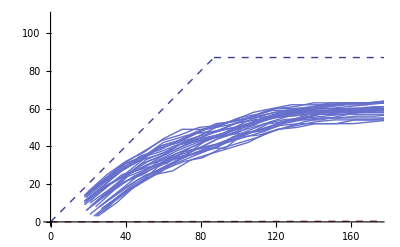
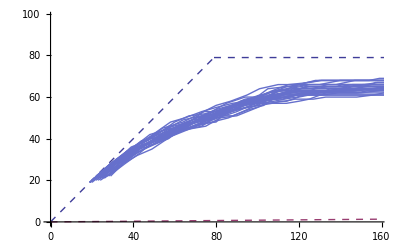
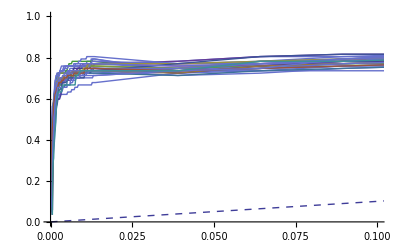
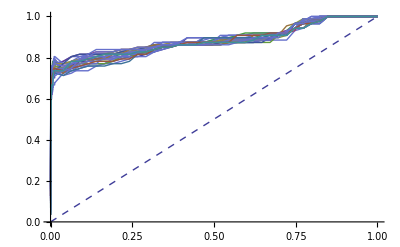
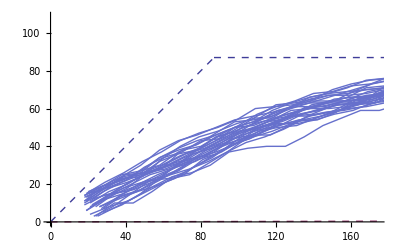
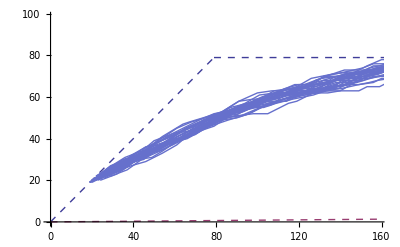
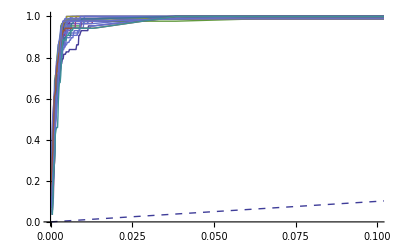
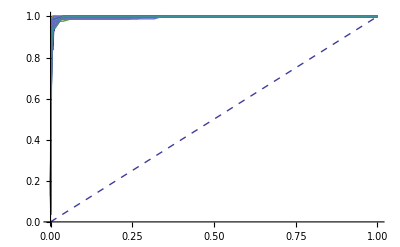
AR | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | Neighborhood
186 prots
1605 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | Neighborhood
186 prots
1605 edges | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | Neighborhood
334 prots
3340 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | Neighborhood
334 prots
3340 edges | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | Neighborhood
344 prots
3183 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | Neighborhood
344 prots
3183 edges | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | HPRD | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | Neighborhood
338 prots
2772 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TNF | Neighborhood
338 prots
2772 edges | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | Neighborhood
242 prots
2469 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | Neighborhood
242 prots
2469 edges | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | Neighborhood
157 prots
1726 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | Neighborhood
157 prots
1726 edges | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 25%Prot,25%Docs | 24 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 25%Prot,25%Docs | 24 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | Neighborhood
208 prots
2133 edges | LSI+STRING | 25%Prot,25%Docs | 23 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | Neighborhood
208 prots
2133 edges | LSI | 25%Prot,25%Docs | 23 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | Neighborhood
328 prots
2920 edges | LSI+STRING | 25%Prot,25%Docs | 21 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | Neighborhood
328 prots
2920 edges | LSI | 25%Prot,25%Docs | 21 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 25%Prot,25%Docs | 22 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 25%Prot,25%Docs | 22 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 25%%Prot,KEGG REFS | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 25%%Prot,KEGG REFS | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 25%Prot,KEGG REFS | 18 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 25%Prot,KEGG REFS | 18 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
PlotForRows[#]&/@talliedCounts
]
```

```mathematica
PlotForRows[talliedCounts[[-1]]]
PlotForRows[talliedCounts[[-2]]]
```

{HSA04012,HPRD,LSI,25%%Prot,KEGG REFS,11,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{HSA04012,HPRD,LSI+STRING,25%%Prot,KEGG REFS,11,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We compare all the variants for HSA04012

```mathematica
hsa04012Rec=GatherBy[Select[counts,#[[1]]=="hsa04012"&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
```

```mathematica
Grid[
PlotForRows[#]&/@hsa04012Rec
]
```

HSA04012 | HPRD | LSI+STRING |  | 4 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI |  | 4 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | Neighborhood
208 prots
2133 edges | LSI+STRING |  | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | Neighborhood
208 prots
2133 edges | LSI |  | 3 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | 25%%Prot,KEGG REFS | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | 25%%Prot,KEGG REFS | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
hsa04010Rec=GatherBy[Select[counts,#[[1]]=="hsa04010"&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[
PlotForRows[#]&/@hsa04010Rec
]
```

HSA04010 | Neighborhood
328 prots
2920 edges | LSI+STRING | 25%Prot,25%Docs | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | Neighborhood
328 prots
2920 edges | LSI | 25%Prot,25%Docs | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 25%Prot,25%Docs | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 25%Prot,25%Docs | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | TF+MEMB | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | 25%Prot,KEGG REFS | 17 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | 25%Prot,KEGG REFS | 17 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Worth comparing N2 to N4?

```mathematica
IL2Rec=GatherBy[Select[counts,#[[1]]=="il2"∧#[[14]]==LSI+STRING&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[
PlotForRows[#]&/@IL2Rec
]
```

IL2 | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | Neighborhood
157 prots
1726 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Show[
{PlotForRows[IL2Rec[[1]],{Black}][[6]],PlotForRows[IL2Rec[[2]],{Red}][[6]]}
]
Show[
{PlotForRows[IL2Rec[[1]],{Black}][[7]],PlotForRows[IL2Rec[[2]],{Red}][[7]]}
]
Show[
{PlotForRows[IL2Rec[[1]],{Black}][[8]],PlotForRows[IL2Rec[[2]],{Red}][[8]]}
]
```

-Graphics-

-Graphics-

-Graphics-

## Worth comparing N1 to N4?

```mathematica
IL2Rec=GatherBy[Select[counts,#[[1]]=="il2"∧#[[14]]==LSI+STRING&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[
PlotForRows[#]&/@IL2Rec
]
```

IL2 | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | Neighborhood
157 prots
1726 edges | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | Neighborhood
43 prots
295 edges | LSI+STRING | 25%Prot,25%Docs | 31 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Worth comparing LSI vs LSI+STRING in whole interactome?

```mathematica
IL2Rec=GatherBy[Select[counts,#[[1]]=="ar"∧#[[6]]>3000&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[
PlotForRows[#]&/@IL2Rec
]
```

AR | HPRD | LSI+STRING | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,25%Docs | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
{Show[
{PlotForRows[IL2Rec[[1]],{Black}][[6]],PlotForRows[IL2Rec[[2]],{Red}][[6]]}
],
Show[
{PlotForRows[IL2Rec[[1]],{Black}][[7]],PlotForRows[IL2Rec[[2]],{Red}][[7]]}
],
Show[
{PlotForRows[IL2Rec[[1]],{Black}][[8]],PlotForRows[IL2Rec[[2]],{Red}][[8]]}
]}}]
```

-Graphics- | -Graphics- | -Graphics-

## Do I find back results comparable to the table?